Define variable:

```mathematica
Needs["PhysicalConstants`"]
Subscript[E, 0]=1.602176487*^-19
m = 0.1*9.10938215*^-31
ℏ = 1.054571628251774*^-34
π = 3.14
T =300
Subscript[k, B]= 1.3806504*^-23
```

1.60218×10^-19

9.10938×10^-32

1.05457×10^-34

Set::wrsym: Symbol π is Protected.

3.14

300

1.38065×10^-23

General Expression:

```mathematica
∫_Subscript[E, 0]^∞ √(2m)/(π*ℏ √(x-Subscript[E, 0]))/(1+Exp[(x-ef)/(Subscript[k, B] T)])ⅆx
```

∫_(1.60218×10^-19)^∞ (1.28835×10^18)/((1+ⅇ^(2.41432×10^20 (-ef+x))) √(-1.60218×10^-19+x))ⅆx

Non-degenerate case:

```mathematica
n1=∫_Subscript[E, 0]^∞ √(2m)/(π*ℏ √(x-Subscript[E, 0]))(Exp[-(x-ef)/(Subscript[k, B] T)])ⅆx
```

2.33329×10^-9 ⅇ^(2.41432×10^20 ef)

Degenerate case:

```mathematica
n2 = ∫_Subscript[E, 0]^ef √(2m)/(π*ℏ √(x-Subscript[E, 0]))ⅆx
```

2.5767×10^18 √(-1.60218×10^-19+ef)

```mathematica
8.148234113094242*^18 √(-1.602176487*^-19+ef)
```

8.14823×10^18 √(-1.60218×10^-19+ef)

Plot the figure:

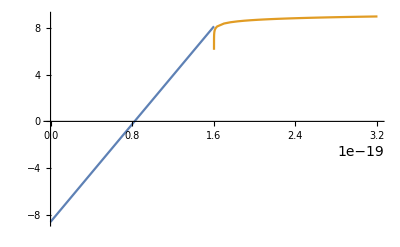

```mathematica
Plot[{ConditionalExpression[Log[10,n1],0≤ef<1*1.602176487*^-19],ConditionalExpression[Log[10,n2],1*1.602176487*^-19<ef≤2*1.602176487*^-19]},{ef,0,2*1.602176487*^-19},BaseStyle->Thickness[.02]]
```